General matrices

```mathematica
P = { {Cos[θ/2], Exp[-ⅈϕ] * Sin[θ/2]}, {Exp[ⅈϕ] * Sin[θ/2], -Cos[θ/2]}};
MatrixForm[P];

Zz = {{1,0},{0,-1}};
Yz= {{0,-ⅈ}, {ⅈ, 0}};
Xz = {{0,1}, {1,0}};



X = {{Cos[ϕ] Sin[θ], -Exp[-ⅈ*ϕ](Cos[θ]Cos[ϕ] + ⅈ*Sin[ϕ])},{-Exp[ⅈ*ϕ](Cos[θ]Cos[ϕ] - ⅈ*Sin[ϕ]),- Cos[ϕ] Sin[θ]}};

Y = {{Sin[θ]Sin[ϕ], -Exp[-ⅈ*ϕ](Cos[θ]Sin[ϕ] - ⅈ*Cos[ϕ])}, {-Exp[ⅈ*ϕ](Cos[θ]Sin[ϕ] + ⅈ*Cos[ϕ]), -Sin[θ]Sin[ϕ]}};
Z = {{Cos[θ], Exp[-ⅈ*ϕ]Sin[θ]}, {Exp[ⅈ*ϕ]Sin[θ], -Cos[θ]}};
Id = {{1,0},{0,1}};
MatrixForm[X] ;
MatrixForm[Y];
MatrixForm[Z];
```

----------------------------------------------------------------------------------
Now, we consider each H_i of the Ising Hamiltonian and find its eigenvalues

```mathematica
Zi = {{Cos[t1], Exp[-ⅈ*p1]Sin[t1]}, {Exp[ⅈ*p1]Sin[t1], -Cos[t1]}};
Zj = {{Cos[t2], Exp[-ⅈ*p2]Sin[t2]}, {Exp[ⅈ*p2]Sin[t2], -Cos[t2]}};
Zk = {{Cos[t3], Exp[-ⅈ*p3]Sin[t3]}, {Exp[ⅈ*p3]Sin[t3], -Cos[t3]}};
```

```mathematica
Xi = {{Cos[p1] Sin[t1], -Exp[-ⅈ*p1](Cos[t1]Cos[p1] + ⅈ*Sin[p1])},{-Exp[ⅈ*p1](Cos[t1]Cos[p1] - ⅈ*Sin[p1]),- Cos[p1] Sin[t1]}};
Xj = {{Cos[p2] Sin[t2], -Exp[-ⅈ*p2](Cos[t2]Cos[p2] + ⅈ*Sin[p2])},{-Exp[ⅈ*p2](Cos[t2]Cos[p2] - ⅈ*Sin[p2]),- Cos[p2] Sin[t2]}};
Xk = {{Cos[p3] Sin[t3], -Exp[-ⅈ*p3](Cos[t3]Cos[p3] + ⅈ*Sin[p3])},{-Exp[ⅈ*p3](Cos[t3]Cos[p3] - ⅈ*Sin[p3]),- Cos[p3] Sin[t3]}};
```

```mathematica
Hi = J KroneckerProduct[Zi,Zj, Id]+J KroneckerProduct[Id,Zj, Zk]+J KroneckerProduct[Zi, Id, Zk]+KroneckerProduct[Xi,Id, Id] + h KroneckerProduct[Id,Xj,Id] + h KroneckerProduct[Id,Id,Xk];

MatrixForm[Hi]
```

(J Cos[t1] Cos[t2]+J Cos[t1] Cos[t3]+J Cos[t2] Cos[t3]+Cos[p1] Sin[t1]+h Cos[p2] Sin[t2]+h Cos[p3] Sin[t3] | -ⅇ^(-ⅈ p3) h (Cos[p3] Cos[t3]+ⅈ Sin[p3])+ⅇ^(-ⅈ p3) J Cos[t1] Sin[t3]+ⅇ^(-ⅈ p3) J Cos[t2] Sin[t3] | -ⅇ^(-ⅈ p2) h (Cos[p2] Cos[t2]+ⅈ Sin[p2])+ⅇ^(-ⅈ p2) J Cos[t1] Sin[t2]+ⅇ^(-ⅈ p2) J Cos[t3] Sin[t2] | ⅇ^(-ⅈ p2-ⅈ p3) J Sin[t2] Sin[t3] | -ⅇ^(-ⅈ p1) (Cos[p1] Cos[t1]+ⅈ Sin[p1])+ⅇ^(-ⅈ p1) J Cos[t2] Sin[t1]+ⅇ^(-ⅈ p1) J Cos[t3] Sin[t1] | ⅇ^(-ⅈ p1-ⅈ p3) J Sin[t1] Sin[t3] | ⅇ^(-ⅈ p1-ⅈ p2) J Sin[t1] Sin[t2] | 0
-ⅇ^(ⅈ p3) h (Cos[p3] Cos[t3]-ⅈ Sin[p3])+ⅇ^(ⅈ p3) J Cos[t1] Sin[t3]+ⅇ^(ⅈ p3) J Cos[t2] Sin[t3] | J Cos[t1] Cos[t2]-J Cos[t1] Cos[t3]-J Cos[t2] Cos[t3]+Cos[p1] Sin[t1]+h Cos[p2] Sin[t2]-h Cos[p3] Sin[t3] | ⅇ^(-ⅈ p2+ⅈ p3) J Sin[t2] Sin[t3] | -ⅇ^(-ⅈ p2) h (Cos[p2] Cos[t2]+ⅈ Sin[p2])+ⅇ^(-ⅈ p2) J Cos[t1] Sin[t2]-ⅇ^(-ⅈ p2) J Cos[t3] Sin[t2] | ⅇ^(-ⅈ p1+ⅈ p3) J Sin[t1] Sin[t3] | -ⅇ^(-ⅈ p1) (Cos[p1] Cos[t1]+ⅈ Sin[p1])+ⅇ^(-ⅈ p1) J Cos[t2] Sin[t1]-ⅇ^(-ⅈ p1) J Cos[t3] Sin[t1] | 0 | ⅇ^(-ⅈ p1-ⅈ p2) J Sin[t1] Sin[t2]
-ⅇ^(ⅈ p2) h (Cos[p2] Cos[t2]-ⅈ Sin[p2])+ⅇ^(ⅈ p2) J Cos[t1] Sin[t2]+ⅇ^(ⅈ p2) J Cos[t3] Sin[t2] | ⅇ^(ⅈ p2-ⅈ p3) J Sin[t2] Sin[t3] | -J Cos[t1] Cos[t2]+J Cos[t1] Cos[t3]-J Cos[t2] Cos[t3]+Cos[p1] Sin[t1]-h Cos[p2] Sin[t2]+h Cos[p3] Sin[t3] | -ⅇ^(-ⅈ p3) h (Cos[p3] Cos[t3]+ⅈ Sin[p3])+ⅇ^(-ⅈ p3) J Cos[t1] Sin[t3]-ⅇ^(-ⅈ p3) J Cos[t2] Sin[t3] | ⅇ^(-ⅈ p1+ⅈ p2) J Sin[t1] Sin[t2] | 0 | -ⅇ^(-ⅈ p1) (Cos[p1] Cos[t1]+ⅈ Sin[p1])-ⅇ^(-ⅈ p1) J Cos[t2] Sin[t1]+ⅇ^(-ⅈ p1) J Cos[t3] Sin[t1] | ⅇ^(-ⅈ p1-ⅈ p3) J Sin[t1] Sin[t3]
ⅇ^(ⅈ p2+ⅈ p3) J Sin[t2] Sin[t3] | -ⅇ^(ⅈ p2) h (Cos[p2] Cos[t2]-ⅈ Sin[p2])+ⅇ^(ⅈ p2) J Cos[t1] Sin[t2]-ⅇ^(ⅈ p2) J Cos[t3] Sin[t2] | -ⅇ^(ⅈ p3) h (Cos[p3] Cos[t3]-ⅈ Sin[p3])+ⅇ^(ⅈ p3) J Cos[t1] Sin[t3]-ⅇ^(ⅈ p3) J Cos[t2] Sin[t3] | -J Cos[t1] Cos[t2]-J Cos[t1] Cos[t3]+J Cos[t2] Cos[t3]+Cos[p1] Sin[t1]-h Cos[p2] Sin[t2]-h Cos[p3] Sin[t3] | 0 | ⅇ^(-ⅈ p1+ⅈ p2) J Sin[t1] Sin[t2] | ⅇ^(-ⅈ p1+ⅈ p3) J Sin[t1] Sin[t3] | -ⅇ^(-ⅈ p1) (Cos[p1] Cos[t1]+ⅈ Sin[p1])-ⅇ^(-ⅈ p1) J Cos[t2] Sin[t1]-ⅇ^(-ⅈ p1) J Cos[t3] Sin[t1]
-ⅇ^(ⅈ p1) (Cos[p1] Cos[t1]-ⅈ Sin[p1])+ⅇ^(ⅈ p1) J Cos[t2] Sin[t1]+ⅇ^(ⅈ p1) J Cos[t3] Sin[t1] | ⅇ^(ⅈ p1-ⅈ p3) J Sin[t1] Sin[t3] | ⅇ^(ⅈ p1-ⅈ p2) J Sin[t1] Sin[t2] | 0 | -J Cos[t1] Cos[t2]-J Cos[t1] Cos[t3]+J Cos[t2] Cos[t3]-Cos[p1] Sin[t1]+h Cos[p2] Sin[t2]+h Cos[p3] Sin[t3] | -ⅇ^(-ⅈ p3) h (Cos[p3] Cos[t3]+ⅈ Sin[p3])-ⅇ^(-ⅈ p3) J Cos[t1] Sin[t3]+ⅇ^(-ⅈ p3) J Cos[t2] Sin[t3] | -ⅇ^(-ⅈ p2) h (Cos[p2] Cos[t2]+ⅈ Sin[p2])-ⅇ^(-ⅈ p2) J Cos[t1] Sin[t2]+ⅇ^(-ⅈ p2) J Cos[t3] Sin[t2] | ⅇ^(-ⅈ p2-ⅈ p3) J Sin[t2] Sin[t3]
ⅇ^(ⅈ p1+ⅈ p3) J Sin[t1] Sin[t3] | -ⅇ^(ⅈ p1) (Cos[p1] Cos[t1]-ⅈ Sin[p1])+ⅇ^(ⅈ p1) J Cos[t2] Sin[t1]-ⅇ^(ⅈ p1) J Cos[t3] Sin[t1] | 0 | ⅇ^(ⅈ p1-ⅈ p2) J Sin[t1] Sin[t2] | -ⅇ^(ⅈ p3) h (Cos[p3] Cos[t3]-ⅈ Sin[p3])-ⅇ^(ⅈ p3) J Cos[t1] Sin[t3]+ⅇ^(ⅈ p3) J Cos[t2] Sin[t3] | -J Cos[t1] Cos[t2]+J Cos[t1] Cos[t3]-J Cos[t2] Cos[t3]-Cos[p1] Sin[t1]+h Cos[p2] Sin[t2]-h Cos[p3] Sin[t3] | ⅇ^(-ⅈ p2+ⅈ p3) J Sin[t2] Sin[t3] | -ⅇ^(-ⅈ p2) h (Cos[p2] Cos[t2]+ⅈ Sin[p2])-ⅇ^(-ⅈ p2) J Cos[t1] Sin[t2]-ⅇ^(-ⅈ p2) J Cos[t3] Sin[t2]
ⅇ^(ⅈ p1+ⅈ p2) J Sin[t1] Sin[t2] | 0 | -ⅇ^(ⅈ p1) (Cos[p1] Cos[t1]-ⅈ Sin[p1])-ⅇ^(ⅈ p1) J Cos[t2] Sin[t1]+ⅇ^(ⅈ p1) J Cos[t3] Sin[t1] | ⅇ^(ⅈ p1-ⅈ p3) J Sin[t1] Sin[t3] | -ⅇ^(ⅈ p2) h (Cos[p2] Cos[t2]-ⅈ Sin[p2])-ⅇ^(ⅈ p2) J Cos[t1] Sin[t2]+ⅇ^(ⅈ p2) J Cos[t3] Sin[t2] | ⅇ^(ⅈ p2-ⅈ p3) J Sin[t2] Sin[t3] | J Cos[t1] Cos[t2]-J Cos[t1] Cos[t3]-J Cos[t2] Cos[t3]-Cos[p1] Sin[t1]-h Cos[p2] Sin[t2]+h Cos[p3] Sin[t3] | -ⅇ^(-ⅈ p3) h (Cos[p3] Cos[t3]+ⅈ Sin[p3])-ⅇ^(-ⅈ p3) J Cos[t1] Sin[t3]-ⅇ^(-ⅈ p3) J Cos[t2] Sin[t3]
0 | ⅇ^(ⅈ p1+ⅈ p2) J Sin[t1] Sin[t2] | ⅇ^(ⅈ p1+ⅈ p3) J Sin[t1] Sin[t3] | -ⅇ^(ⅈ p1) (Cos[p1] Cos[t1]-ⅈ Sin[p1])-ⅇ^(ⅈ p1) J Cos[t2] Sin[t1]-ⅇ^(ⅈ p1) J Cos[t3] Sin[t1] | ⅇ^(ⅈ p2+ⅈ p3) J Sin[t2] Sin[t3] | -ⅇ^(ⅈ p2) h (Cos[p2] Cos[t2]-ⅈ Sin[p2])-ⅇ^(ⅈ p2) J Cos[t1] Sin[t2]-ⅇ^(ⅈ p2) J Cos[t3] Sin[t2] | -ⅇ^(ⅈ p3) h (Cos[p3] Cos[t3]-ⅈ Sin[p3])-ⅇ^(ⅈ p3) J Cos[t1] Sin[t3]-ⅇ^(ⅈ p3) J Cos[t2] Sin[t3] | J Cos[t1] Cos[t2]+J Cos[t1] Cos[t3]+J Cos[t2] Cos[t3]-Cos[p1] Sin[t1]-h Cos[p2] Sin[t2]-h Cos[p3] Sin[t3])

```mathematica
Simplify[Eigenvalues[Hi]]
```

---------------------------------------------------------------------------------------------------------------------
Now, general Kronecker product

```mathematica
v1 = {Cos[t1/2], Exp[ⅈ*p1]Sin[t1/2]};
v2= {Cos[t2/2], Exp[ⅈ*p2]Sin[t2/2]};
v3 = {Cos[t3/2], Exp[ⅈ*p3]Sin[t3/2]};
MatrixForm[KroneckerProduct[v1, v2, v3]]
```

(Cos[t1/2] Cos[t2/2] Cos[t3/2] | ⅇ^(ⅈ p3) Cos[t1/2] Cos[t2/2] Sin[t3/2] | ⅇ^(ⅈ p2) Cos[t1/2] Cos[t3/2] Sin[t2/2] | ⅇ^(ⅈ p2+ⅈ p3) Cos[t1/2] Sin[t2/2] Sin[t3/2]
ⅇ^(ⅈ p1) Cos[t2/2] Cos[t3/2] Sin[t1/2] | ⅇ^(ⅈ p1+ⅈ p3) Cos[t2/2] Sin[t1/2] Sin[t3/2] | ⅇ^(ⅈ p1+ⅈ p2) Cos[t3/2] Sin[t1/2] Sin[t2/2] | ⅇ^(ⅈ p1+ⅈ p2+ⅈ p3) Sin[t1/2] Sin[t2/2] Sin[t3/2])

```mathematica
v12 = {Cos[t1/2]Cos[t2/2], Cos[t1/2]Exp[ⅈ*p2]Sin[t2/2], Exp[ⅈ*p1]Sin[t1/2]Cos[t2/2], Exp[ⅈ*p1]Sin[t1/2]Exp[ⅈ*p2]Sin[t2/2]};
MatrixForm[v12]
```

(Cos[t1/2] Cos[t2/2]
ⅇ^(ⅈ p2) Cos[t1/2] Sin[t2/2]
ⅇ^(ⅈ p1) Cos[t2/2] Sin[t1/2]
ⅇ^(ⅈ p1+ⅈ p2) Sin[t1/2] Sin[t2/2])

```mathematica
Solve[{0,1/Sqrt[2],-1/Sqrt[2],0} == v12, {t1, t2, p1, p2}]
```

{}

```mathematica
t1 = π;
t2 = 0;
v12
```

```mathematica
Clear[t1, t2]
Solve[{Sin[(t1-t2)/2] + Sin[(t1+t2)/2], Sin[(t1-t2)/2] - Sin[(t1+t2)/2]}== {0,0}, {t1, t2}, Reals]
```

{{t1→ConditionalExpression[2 π C[1]+2 π C[2], (C[1]|C[2])∈ℤ],t2→ConditionalExpression[-2 π C[1]+2 π C[2], (C[1]|C[2])∈ℤ]},{t1→ConditionalExpression[π+2 π C[1]+2 π C[2], (C[1]|C[2])∈ℤ],t2→ConditionalExpression[-π-2 π C[1]+2 π C[2], (C[1]|C[2])∈ℤ]},{t1→ConditionalExpression[π+2 π C[1]+2 π C[2], (C[1]|C[2])∈ℤ],t2→ConditionalExpression[π-2 π C[1]+2 π C[2], (C[1]|C[2])∈ℤ]},{t1→ConditionalExpression[2 π+2 π C[1]+2 π C[2], (C[1]|C[2])∈ℤ],t2→ConditionalExpression[-2 π C[1]+2 π C[2], (C[1]|C[2])∈ℤ]}}

----------------------------------------------------------------------------------------------------------------
Now, equivalence between up and down kets

```mathematica
Clear[t1, t2, p1, p2]
chip = {Cos[t1/2], Exp[ⅈ*p1]Sin[t1/2]};
chim = {Exp[-ⅈ*p2]Sin[t2/2], -Cos[t2/2]}
Solve[chim == c*chip, {t2, p2}]
```

{ⅇ^(-ⅈ p2) Sin[t2/2],-Cos[t2/2]}

{{t2→-2 ArcCos[-ⅇ^(ⅈ p1) Sin[t1/2]],p2→-ⅈ Log[-√(Sec[t1/2]^2-ⅇ^(2 ⅈ p1) Tan[t1/2]^2)]},{t2→-2 ArcCos[-ⅇ^(ⅈ p1) Sin[t1/2]],p2→-ⅈ Log[√(Sec[t1/2]^2-ⅇ^(2 ⅈ p1) Tan[t1/2]^2)]},{t2→2 ArcCos[-ⅇ^(ⅈ p1) Sin[t1/2]],p2→-ⅈ Log[-√(Sec[t1/2]^2-ⅇ^(2 ⅈ p1) Tan[t1/2]^2)]},{t2→2 ArcCos[-ⅇ^(ⅈ p1) Sin[t1/2]],p2→-ⅈ Log[√(Sec[t1/2]^2-ⅇ^(2 ⅈ p1) Tan[t1/2]^2)]}}

```mathematica
t1 = π/2;
p1 = π;
t2= -2 ArcCos[-c ⅇ^(ⅈ p1) Sin[t1/2]]
p2 = TrigReduce[-ⅈ Log[-(√(Sec[t1/2]^2-c^2 ⅇ^(2 ⅈ p1) Tan[t1/2]^2))/c]]
MatrixForm[chip]
Clear[c]; c=1
MatrixForm[chim]
```

-π/2

π

(1/(√2)
-1/(√2))

1

(1/(√2)
-1/(√2))

```mathematica
plus = {{Cos[θ/2]}, {Exp[ⅈϕ]Sin[θ/2]}};
moins = {{Exp[-ⅈϕ]Sin[θ/2]},{-Cos[θ/2]}};
ConjugateTranspose[moins].Z.moins
```

```mathematica
{{ⅇ^-ⅈϕ Sin[θ/2] (-ⅇ^(ⅈ ϕ) Cos[Conjugate[θ]/2] Sin[θ]+ⅇ^(-Conjugate[ⅈϕ]) Cos[θ] Sin[Conjugate[θ]/2])-Cos[θ/2] (Cos[θ] Cos[Conjugate[θ]/2]+ⅇ^(-ⅈ ϕ-Conjugate[ⅈϕ]) Sin[θ] Sin[Conjugate[θ]/2])}}
```

test psi(theta)

```mathematica
up = {{1}, {0}};
down = {{0}, {1}};

P1 = { {Cos[θ1/2], Exp[-ⅈϕ1] * Sin[θ1/2]}, {Exp[ⅈϕ1] * Sin[θ1/2], -Cos[θ1/2]}};
P2 = { {Cos[θ2/2], Exp[-ⅈϕ2] * Sin[θ2/2]}, {Exp[ⅈϕ2] * Sin[θ2/2], -Cos[θ2/2]}};
P3 = { {Cos[θ3/2], Exp[-ⅈϕ3] * Sin[θ3/2]}, {Exp[ⅈϕ3] * Sin[θ3/2], -Cos[θ3/2]}};
P4 = { {Cos[θ4/2], Exp[-ⅈϕ4] * Sin[θ4/2]}, {Exp[ⅈϕ4] * Sin[θ4/2], -Cos[θ4/2]}};
P = KroneckerProduct[P1, P2];

chip1 = {{Cos[t1/2]}, {Exp[ⅈ*p1]Sin[t1/2]}};
chim1 = {{Exp[-ⅈ*p1]Sin[t1/2]}, {-Cos[t1/2]}};

chip2 = {{Cos[t2/2]}, {Exp[ⅈ*p2]Sin[t2/2]}};
chim2 = {{Exp[-ⅈ*p2]Sin[t2/2]}, {-Cos[t2/2]}};


psi = (KroneckerProduct[up, down] + KroneckerProduct[up, up])/Sqrt[2];
MatrixForm[P.psi];


Simplify[TrigReduce[chip1 + ⅈ*chim1]]
```

{{Cos[t1/2]+ⅈ ⅇ^(-ⅈ p1) Sin[t1/2]},{-ⅈ Cos[t1/2]+ⅇ^(ⅈ p1) Sin[t1/2]}}

```mathematica
MatrixForm[ConjugateTranspose[ KroneckerProduct[chip1, chip1]] .KroneckerProduct[chim1, chim1]]// TrigExpand
```

(ⅇ^(-2 ⅈ p1) Cos[Conjugate[t1]/2]^2 Sin[t1/2]^2-2 ⅇ^(-ⅈ p1-ⅈ Conjugate[p1]) Cos[t1/2] Cos[Conjugate[t1]/2] Sin[t1/2] Sin[Conjugate[t1]/2]+ⅇ^(-2 ⅈ Conjugate[p1]) Cos[t1/2]^2 Sin[Conjugate[t1]/2]^2)

```mathematica
ket[t1_, p1_, t2_, p2_] ={{Cos[t1/2]Cos[t2/2]},{Exp[ⅈ*p2]Cos[t1/2]Sin[t2/2]},{Exp[ⅈ*p1]Cos[t2/2]Sin[t1/2]},{Exp[ⅈ*p1 + ⅈ*p2]Sin[t1/2]Sin[t2/2]}};
bra[t1_, p1_, t2_, p2_] =Refine [ConjugateTranspose[{{Cos[t1/2]Cos[t2/2]},{Exp[ⅈ*p2]Cos[t1/2]Sin[t2/2]},{Exp[ⅈ*p1]Cos[t2/2]Sin[t1/2]},{Exp[ⅈ*p1 + ⅈ*p2]Sin[t1/2]Sin[t2/2]}}],{Element[t1, Reals], Element[t2, Reals], Element[p1, Reals], Element[p2, Reals]}];
Simplify[TrigReduce[bra[t1, p1, t2, p2].ket[π-t1, π+p1,π-t2,π+p2]]]


Simplify[TrigReduce[Refine [ConjugateTranspose[Chi[t1, p1, t2, p2]].Chi[π-t1, π+p1,π-t2,π+p2],{Element[t1, Reals], Element[t2, Reals], Element[p1, Reals], Element[p2, Reals]}]]]
```

{{0}}

{{-1/4 (-1+ⅇ^(ⅈ p1+Conjugate[ⅈp1])+ⅇ^(ⅈ p2+Conjugate[ⅈp2])-ⅇ^(ⅈ (p1+p2)+Conjugate[ⅈp1+ⅈp2])) Sin[t1] Sin[t2]}}

```mathematica
Solve[{Cos[x/2], Sin[x/2]} == {Sin[y/2 + π/6], -Cos[y/2 + π/6]}, {x}]
```

{{x→ConditionalExpression[2 (ArcTan[Sin[π/6+y/2],-Cos[π/6+y/2]]+2 π C[1]), C[1]∈ℤ]}}

```mathematica
Hz = J KroneckerProduct[Zz,Zz] + J KroneckerProduct[Yz,Yz] + J KroneckerProduct[Xz,Xz];
MatrixForm[Hz];
Eigenvectors[Hz]
Eigenvalues[Hz]
```

{{0,-1,1,0},{0,0,0,1},{0,1,1,0},{1,0,0,0}}

{-3 J,J,J,J}

```mathematica
Hz.{1,-(J+√(4 h^2+J^2))/(2 h),-(J+√(4 h^2+J^2))/(2 h),1}
```

{-√(4 h^2+J^2),2 h+(J (J+√(4 h^2+J^2)))/(2 h),2 h+(J (J+√(4 h^2+J^2)))/(2 h),-√(4 h^2+J^2)}

```mathematica
Sz = KroneckerProduct[Zz, Id]+ KroneckerProduct[Id, Zz]; 
psi = {{a},{b},{c},{d}};
Clear[t1,t2,p1,p2]
MatrixForm[Sz.v12]
```

(2 Cos[t1/2] Cos[t2/2]
0
0
-2 ⅇ^(ⅈ p1+ⅈ p2) Sin[t1/2] Sin[t2/2])

```mathematica
t1= π+t2;
TrigReduce[ConjugateTranspose[v12].Sz.v12]
MatrixForm[TrigReduce[v12]];
```

1/4 (-1+ⅇ^(2 ⅈ p1+2 ⅈ p2)) (-1+Cos[2 t2])

2 Cos[t2/2]^2 Cos[(π+t2)/2]^2-2 ⅇ^(2 ⅈ p1+2 ⅈ p2) Sin[t2/2]^2 Sin[(π+t2)/2]^2

{2 Cos[t2/2] Cos[(π+t2)/2],0,0,-2 ⅇ^(ⅈ p1+ⅈ p2) Sin[t2/2] Sin[(π+t2)/2]}

{2 Cos[t1/2] Cos[t2/2],0,0,-2 ⅇ^(ⅈ p1+ⅈ p2) Sin[t1/2] Sin[t2/2]}

{{a},{b},{-b},{-a}}

```mathematica
Sz = KroneckerProduct[Zz,Id,Id,Id]+ KroneckerProduct[Id,Zz,Id,Id]+ KroneckerProduct[Id,Id,Zz,Id]+ KroneckerProduct[Id,Id,Id,Zz];
Clear[t1, t2, t3, t4, p1, p2, p3, p4]
v1 = {{Cos[t1/2]}, {Exp[ⅈ*p1]Sin[t1/2]}};
v2= {{Cos[t2/2]}, {Exp[ⅈ*p2]Sin[t2/2]}};
v3 = {{Cos[t3/2]}, {Exp[ⅈ*p3]Sin[t3/2]}};
v4 = {{Cos[t4/2]}, {Exp[ⅈ*p4]Sin[t4/2]}};
v1234 = KroneckerProduct[v1, v2, v3, v4];
t1 = π/2;
p1 = 0;
t2 = π/2;
p2 = π;
t3 = 3π/2;
p3 = π/4;
t4 = 3π/2;
p4 = 3π/4;
MatrixForm[Sz.v1234]
* Solve[Sz.v1234 == {{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}, {t1,t2,t3,t4,p1,p2,p3,p4}] *
```

(1
-1/2 ⅇ^((3 ⅈ π)/4)
-1/2 ⅇ^((ⅈ π)/4)
0
-1/2
0
0
-1/2
1/2
0
0
1/2
0
1/2 ⅇ^(-(ⅈ π)/4)
1/2 ⅇ^(-(3 ⅈ π)/4)
-1)

```mathematica
Magnetization[t1_,t2_,t3_,t4_,p1_,p2_,p3_,p4_] = (KroneckerProduct[Zz,Id,Id,Id]+ KroneckerProduct[Id,Zz,Id,Id]+ KroneckerProduct[Id,Id,Zz,Id]+ KroneckerProduct[Id,Id,Id,Zz]).KroneckerProduct[{{Cos[t1/2]}, {Exp[ⅈ*p1]Sin[t1/2]}}, {{Cos[t2/2]}, {Exp[ⅈ*p2]Sin[t2/2]}}, {{Cos[t3/2]}, {Exp[ⅈ*p3]Sin[t3/2]}}, {{Cos[t4/2]}, {Exp[ⅈ*p4]Sin[t4/2]}}];
m1 = Magnetization[0,0,π,π/2, p1,p2,p3,p4];
m2 = Magnetization[0,0,π,π/2, p1,p2,p3,p4+π];
MatrixForm[Simplify[TrigReduce[m1 + m2]]];
```

(2
-(-1)^(3/4)
-(-1)^(1/4)
0
-1
0
0
-1
1
0
0
1
0
-(-1)^(3/4)
-(-1)^(1/4)
-2)

```mathematica
({{0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}})
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
Clear[p1,p2,t1,t2]
MatrixForm[v12];
Solve[{∫_0^π ∫_0^π ∫_0^(2π) ∫_0^(2π) Psi[t1, t2, p1, p2]Cos[t1/2]Cos[t2/2] ⅆp1 ⅆp2ⅆt1ⅆt2, ∫_0^π ∫_0^π ∫_0^(2π) ∫_0^(2π) Psi[t1, t2, p1, p2]Sin[t1/2]Sin[t2/2] ⅇ^(ⅈ (p1+p2))ⅆp1 ⅆp2ⅆt1ⅆt2} == {0,0}, Psi[t1_, t2_, p1_, p2_]]
```

Solve::ivar: Sin[t1_/2] Sin[t2_/2] is not a valid variable.

Solve[False,Sin[t1_/2] Sin[t2_/2]]

Sin[t1] Sin[t2]

(64 π^2)/9

```mathematica
Psi[t1_, t2_, p1_, p2_] = (t1-t2)^3;
∫_0^π ∫_0^π ∫_0^(2π) ∫_0^(2π) Psi[t1, t2, p1, p2]Sin[t1/2]Sin[t2/2]  ⅆp1 ⅆp2ⅆt1ⅆt2
TrigReduce[Sin[t1/2]Cos[t2/2] - Cos[t1/2]Sin[t2/2]];
```

0

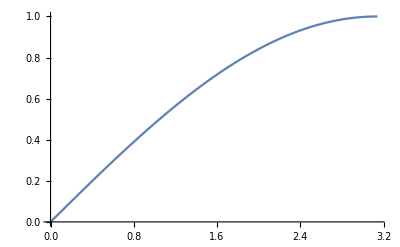

```mathematica
Plot[Sin[x/2],{x,0,Pi}]
```

```mathematica
Plot3D[{Sin[x-y], Sin[π-x+y]},{x,0,π},{y,0,π}]
```

-Graphics3D-